## Телица Илья Денисович гр. 221701 Вариант 12

### Задание 1

```mathematica
При n = 6
```

Lg=  0.+11.9425 x-6.17804 x^2+0.776496 x^3+0.114566 x^4-0.0331094 x^5+0.00203712 x^6

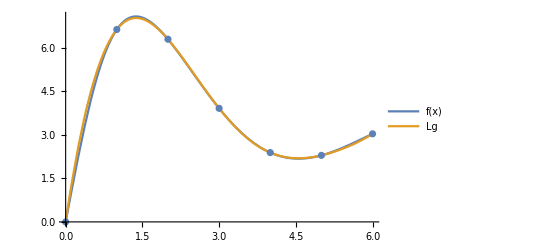

```mathematica
f[x_]:=(7*x+12*Sin[x])/(√(π+x^2+((1+x^2)^4)^(1/3))) ;L=0;R=6;n=6;h=(R-L)/n;
(*Задание начальных условий*)
data=N[Table[{L+i*h,f[L+i*h]},{i,0,n}]];
(*Создание таблицы аргументов и значений функции с заданным шагом*)
Lagrange[x_]=∑_(i=1)^(n+1) data[[i,2]]*∏_(j=1)^(n+1) If[i!=j,(x-data[[j,1]])/(data[[i,1]]-data[[j,1]]),1];
(*Задание функции для постоения интерполяционного многочлена Лагранжа*)
Echo[Lg=Lagrange[x]//Simplify,"Lg="];
(*Расчет интерполяционного многочлена Лагранжа для заданной функции*)
Show[Plot[{f[x],Lg},{x,L,R},PlotLegends->"Expressions"],ListPlot[data]]
(*Графическое представление исходной функции, многочлена Лагранжа и заданных точек*)
```

```mathematica
Array[dif,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
For[i=n,i>=n-k,i--,dif[i,k]=""]];
(*Заполнение пустыми значениями элементов ниже побочной диагонали*)
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
(*Задание опорных элементов*)
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
dif[i,k]=dif[i+1,k-1]-dif[i,k-1]]];
(*Расчет раздеренной разности, начиная с опорных элементов*)
tab=Array[dif,{n+1,n+1},{0,0}];
(*Создание таблицы разделенных разностей*)
PaddedForm[TableForm[tab],{6,5}]
(*Вывод таблицы*)
```

0.00000 |  6.62449 | -6.96016 |  4.91701 | -2.01875 | -0.30631 |  1.46673
 6.62449 | -0.33567 | -2.04316 |  2.89826 | -2.32505 |  1.16042 | 
 6.28882 | -2.37883 |  0.85510 |  0.57321 | -1.16463 |  | 
 3.90999 | -1.52372 |  1.42831 | -0.59142 |  |  | 
 2.38627 | -0.09541 |  0.83689 |  |  |  | 
 2.29086 |  0.74148 |  |  |  |  | 
 3.03234 |  |  |  |  |  |

0.+11.9425 x-6.17804 x^2+0.776496 x^3+0.114566 x^4-0.0331094 x^5+0.00203712 x^6

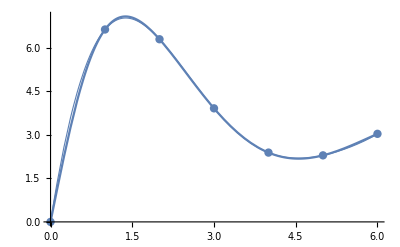

```mathematica
t=(x-L)/h;pn1[x_]=dif[0,0];p[t_]=1;
For[k=1,k<=n,k++,
p[t_]=p[t]*(t-k+1);
pn1[x_]=pn1[x]+dif[0,k]/(k!)*p[t]];
pn1[x]//Simplify
(*Нахождение и вывод первого интерполяционного многочлена Ньютона*)
gr1=Plot[f[x],{x,L,R}];
gr2=ListPlot[data,PlotStyle->PointSize[0.015]];
gr3=Plot[pn1[x],{x,L,R},PlotStyle->Thickness[0.0020]];
Show[gr1,gr2,gr3]
(*Посторение и вывод графика интерполяционного многочлена Ньютона*)
```

```mathematica
Np[x_]=InterpolatingPolynomial[data,x];
Np[x_]=Simplify[Np[x]]
gr4=Plot[Np[x],{x,L,R},PlotStyle->Thickness[0.0020]];
Show[gr1,gr2,gr4]
(*Построение и вывод интерполяционного многочлена Ньютона с помощью встроенной функции*)
```

4.44089×10^-16+11.9425 x-6.17804 x^2+0.776496 x^3+0.114566 x^4-0.0331094 x^5+0.00203712 x^6

-Graphics-

```mathematica
{f[2.4316],Lagrange[2.4316],pn1[2.4316],Np[2.4316]}
(*Вычисление значений функции и всех построенных интерполяционных многочленов в точке х=2,4316*)
```

{5.26999,5.28633,5.28633,5.28633}

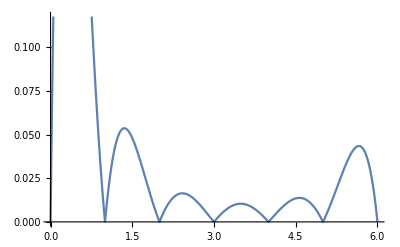

{0.342682,{x→0.310191}}

```mathematica
r[x_]=Abs[f[x]-Np[x]];
Plot[r[x],{x,L,R}]
(*Посторение и вывод графика погрешности интерполирования многочлена Ньютона*)
FindMaximum[r[x],{x,L,R}]
(*Нахождение максимума абсолютных погрешнойстей на отрезке*)
```

```mathematica
При n = 10
```

Lg=  0.+8.70363 x+3.31296 x^2-10.6292 x^3+7.66745 x^4-3.124 x^5+0.823541 x^6-0.143155 x^7+0.0158615 x^8-0.00101624 x^9+0.0000286744 x^10

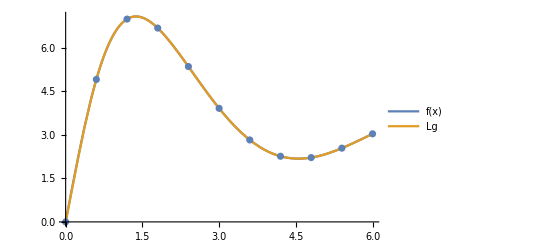

```mathematica
n=10;h=(R-L)/n;
(*Задание начальных условий, т.к. функция и границы уже заданы*)
data=N[Table[{L+i*h,f[L+i*h]},{i,0,n}]];
(*Создание таблицы аргументов и значений функции с заданным шагом*)
Lagrange[x_]=∑_(i=1)^(n+1) data[[i,2]]*∏_(j=1)^(n+1) If[i!=j,(x-data[[j,1]])/(data[[i,1]]-data[[j,1]]),1];
(*Задание функции для постоения интерполяционного многочлена Лагранжа*)
Echo[Lg=Lagrange[x]//Simplify,"Lg="];
(*Расчет интерполяционного многочлена Лагранжа для заданной функции*)
Show[Plot[{f[x],Lg},{x,L,R},PlotLegends->"Expressions"],ListPlot[data]]
(*Графическое представление исходной функции, многочлена Лагранжа и заданных точек*)
```

```mathematica
Array[dif,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
For[i=n,i>=n-k,i--,dif[i,k]=""]];
(*Заполнение пустыми значениями элементов ниже побочной диагонали*)
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
(*Задание опорных элементов*)
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
dif[i,k]=dif[i+1,k-1]-dif[i,k-1]]];
(*Расчет разделенной разности, начиная с опорных элементов*)
tab=Array[dif,{n+1,n+1},{0,0}];
(*Создание таблицы разделенных разностей*)
PaddedForm[TableForm[tab],{6,5}]
(*Вывод таблицы*)
```

0.00000 |  4.90438 | -2.82608 |  0.43851 |  0.93346 | -1.40342 |  1.43437 | -1.30989 |  1.11928 | -0.88511 |  0.62917
 4.90438 |  2.07829 | -2.38758 |  1.37197 | -0.46996 |  0.03095 |  0.12448 | -0.19061 |  0.23417 | -0.25594 | 
 6.98267 | -0.30928 | -1.01561 |  0.90201 | -0.43901 |  0.15543 | -0.06613 |  0.04355 | -0.02177 |  | 
 6.67339 | -1.32490 | -0.11361 |  0.46300 | -0.28357 |  0.08930 | -0.02258 |  0.02178 |  |  | 
 5.34850 | -1.43850 |  0.34939 |  0.17943 | -0.19427 |  0.06672 | -0.00080 |  |  |  | 
 3.90999 | -1.08911 |  0.52882 | -0.01485 | -0.12755 |  0.06592 |  |  |  |  | 
 2.82088 | -0.56029 |  0.51397 | -0.14240 | -0.06164 |  |  |  |  |  | 
 2.26059 | -0.04632 |  0.37158 | -0.20403 |  |  |  |  |  |  | 
 2.21428 |  0.32526 |  0.16754 |  |  |  |  |  |  |  | 
 2.53954 |  0.49280 |  |  |  |  |  |  |  |  | 
 3.03234 |  |  |  |  |  |  |  |  |  |

0.+8.70363 x+3.31296 x^2-10.6292 x^3+7.66745 x^4-3.124 x^5+0.823541 x^6-0.143155 x^7+0.0158615 x^8-0.00101624 x^9+0.0000286744 x^10

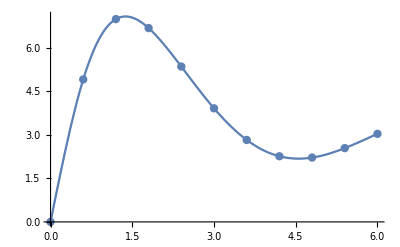

```mathematica
t=(x-L)/h;pn1[x_]=dif[0,0];p[t_]=1;
For[k=1,k<=n,k++,
p[t_]=p[t]*(t-k+1);
pn1[x_]=pn1[x]+dif[0,k]/(k!)*p[t]];
pn1[x]//Simplify
(*Нахождение и вывод первого интерполяционного многочлена Ньютона*)
gr1=Plot[f[x],{x,L,R}];
gr2=ListPlot[data,PlotStyle->PointSize[0.015]];
gr3=Plot[pn1[x],{x,L,R},PlotStyle->Thickness[0.0020]];
Show[gr1,gr2,gr3]
(*Вывод графика интерполяционного многочлена Ньютона*)
```

```mathematica
Np[x_]=InterpolatingPolynomial[data,x];
Np[x_]=Simplify[Np[x]]
gr4=Plot[Np[x],{x,L,R},PlotStyle->Thickness[0.0020]];
Show[gr1,gr2,gr4]
(*Построение и вывод интерполяционного многочлена Ньютона с помощью встроенной функции*)
```

4.44089×10^-16+8.70363 x+3.31296 x^2-10.6292 x^3+7.66745 x^4-3.124 x^5+0.823541 x^6-0.143155 x^7+0.0158615 x^8-0.00101624 x^9+0.0000286744 x^10

-Graphics-

```mathematica
{f[2.4316],Lagrange[2.4316],pn1[2.4316],Np[2.4316]}
(*Вычисление значений функции и всех построенных интерполяционных многочленов в точке х=2,4316*)
```

{5.26999,5.26999,5.26999,5.26999}

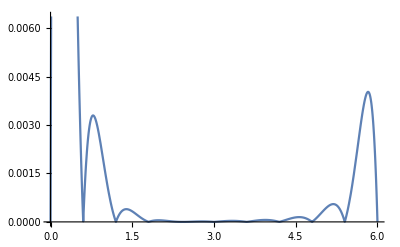

{0.0405509,{x→0.159605}}

```mathematica
r[x_]=Abs[f[x]-Np[x]];
Plot[r[x],{x,L,R}]
(*Посторение и вывод графика погрешности интерполирования многочлена Ньютона*)
FindMaximum[r[x],{x,L,R}]
(*Нахождение максимума абсолютных погрешнойстей на отрезке*)
```

#### ж) чем больше узлов интерполяции, тем ниже погрешность интерполирования .

### Задание 2

```mathematica
При n = 6
```

Set::write: Tag Times in При n is Protected.

6

```mathematica
n=6;
T={t1,t2,t3,t4,t5,t6};
X={x1,x2,x3,x4,x5,x6};
For[i=0,i<=n,i++,T[[i]]=Cos[(Pi*(2*i+1))/(2*n+2)];X[[i]]=(L+R)/2+(R-L)/2*T[[i]]];
data=N[Table[{X[[i]],f[X[[i]]]},{i,0,n}]]
(*Задание начальных условий*)
```

{{5.92478,2.96864},{5.34549,2.49984},{4.30165,2.21924},{3.,3.90999},{1.69835,6.83037},{0.654506,5.22344},{0.0752163,0.700699}}

```mathematica
Array[dif{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
For[i=n,i>=n-k,i--,dif[i,k]=""]];
(*Заполнение пустыми значениями элементов ниже побочной диагонали*)
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
(*Задание опорных элементов*)
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
dif[i,k]=dif[i+1,k-1]-dif[i,k-1]]];
(*Расчет разделенной разности, начиная с опорных элементов*)
tab=Array[dif,{n+1,n+1},{0,0}];
(*Создание таблицы разделенных разностей*)
PaddedForm[TableForm[tab],{6,5}]
(*Вывод таблицы*)
```

2.96864 | -0.46880 |  0.18820 |  1.78315 | -2.52487 | -2.49036 |  14.87400
 2.49984 | -0.28060 |  1.97135 | -0.74172 | -5.01522 |  12.38370 | 
 2.21924 |  1.69075 |  1.22963 | -5.75694 |  7.36844 |  | 
 3.90999 |  2.92038 | -4.52731 |  1.61150 |  |  | 
 6.83037 | -1.60693 | -2.91581 |  |  |  | 
 5.22344 | -4.52274 |  |  |  |  | 
 0.70070 |  |  |  |  |  |

3.00413-0.463158 x-0.282135 x^2+2.27531 x^3-0.326045 x^4-9.20297 x^5+14.874 x^6

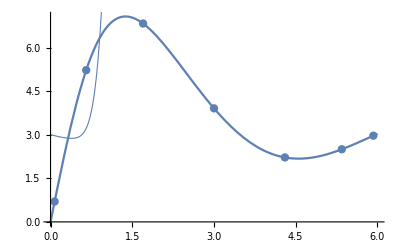

```mathematica
q=Table[dif[i,k],{i,0,n},{k,1,n}];
Pnr[x_]=data[[1,2]]+∑_(i=1)^n q[[1,i]]*∏_(j=1)^i (x-data[[k,1]])//Simplify
(*Нахождение интерполяционного многочлена Ньютона для неравноотстоящих узлов*)
gr1=Plot[f[x],{x,L,R}];
gr2=ListPlot[data,PlotStyle->PointSize[0.015]];
gr3=Plot[Pnr[x],{x,L,R},PlotStyle->Thickness[0.0020]];
Show[gr1,gr2,gr3]
(*Вывод графика интерполяционного многочлена Ньютона*)
```

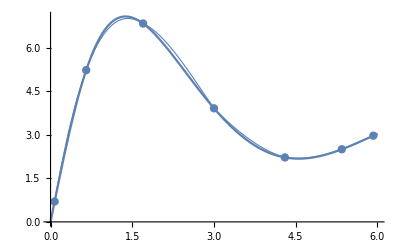

```mathematica
Intf=Interpolation[data];
gr4=Plot[Intf[x],{x,data[[7,1]],6},PlotStyle->Thickness[0.002]];
Show[gr1,gr2,gr4]
(*Построение и вывод интерполирующей фунции при помощи встроенной функции*)
```

```mathematica
{f[2.4316],Pnr[2.4316],Intf[2.4316]}
(*Вычисление значений функции и всех построенных интерполяционных многочленов в точке х=2,4316*)
```

{5.26999,2313.74,5.45624}

```mathematica
FindMaximum[Abs[f[x]-Intf[x]],{x,1,R}](*Нахождение максимума абсолютных погрешнойстей на отрезке*)
```

{0.112566,{x→1.07736}}

```mathematica
При n = 10
```

```mathematica
n=10;
T={t1,t2,t3,t4,t5,t6,t7,t8,t9,t10};
X={x1,x2,x3,x4,x5,x6,x7,x8,x9,x10};
For[i=0,i<=n,i++,T[[i]]=Cos[(Pi*(2*i+1))/(2*n+2)];X[[i]]=(L+R)/2+(R-L)/2*T[[i]]];
data=N[Table[{X[[i]],f[X[[i]]]},{i,0,n}]]
(*Задание начальных условий*)
```

{{5.96946,3.00653},{5.7289,2.80258},{5.26725,2.4456},{4.62192,2.18105},{3.8452,2.52522},{3.,3.90999},{2.1548,5.94274},{1.37808,7.07322},{0.732751,5.6344},{0.271104,2.46079},{0.0305357,0.284984}}

```mathematica
Array[dif{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
For[i=n,i>=n-k,i--,dif[i,k]=""]];
(*Заполнение пустыми значениями элементов ниже побочной диагонали*)
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
(*Задание опорных элементов*)
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
dif[i,k]=dif[i+1,k-1]-dif[i,k-1]]];
(*Расчет разделенной разности, начиная с опорных элементов*)
tab=Array[dif,{n+1,n+1},{0,0}];
(*Создание таблицы разделенных разностей*)
PaddedForm[TableForm[tab],{6,5}]
(*Вывод таблицы*)
```

3.00653 | -0.20396 | -0.15302 |  0.24546 |  0.27081 | -0.35520 | -0.38492 |  0.79192 |  0.17508 | -0.93865 | -3.30040
 2.80258 | -0.35698 |  0.09244 |  0.51627 | -0.08438 | -0.74012 |  0.40700 |  0.96700 | -0.76357 | -4.23905 | 
 2.44560 | -0.26454 |  0.60871 |  0.43189 | -0.82451 | -0.33313 |  1.37400 |  0.20343 | -5.00262 |  | 
 2.18105 |  0.34417 |  1.04060 | -0.39262 | -1.15764 |  1.04087 |  1.57743 | -4.79919 |  |  | 
 2.52522 |  1.38477 |  0.64798 | -1.55026 | -0.11677 |  2.61830 | -3.22176 |  |  |  | 
 3.90999 |  2.03275 | -0.90227 | -1.66702 |  2.50153 | -0.60346 |  |  |  |  | 
 5.94274 |  1.13048 | -2.56930 |  0.83451 |  1.89807 |  |  |  |  |  | 
 7.07322 | -1.43882 | -1.73479 |  2.73258 |  |  |  |  |  |  | 
 5.63440 | -3.17361 |  0.99780 |  |  |  |  |  |  |  | 
 2.46079 | -2.17581 |  |  |  |  |  |  |  |  | 
 0.28498 |  |  |  |  |  |  |  |  |  |

3.01261-0.193956 x-0.173898 x^2+0.209313 x^3+0.318887 x^4-0.26953 x^5-0.547984 x^6+0.728921 x^7+0.294557 x^8+0.0691521 x^9-3.3004 x^10

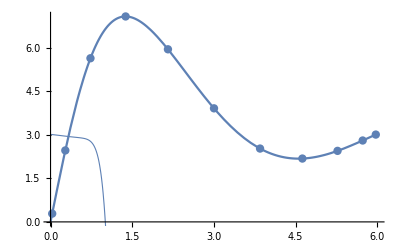

```mathematica
q=Table[dif[i,k],{i,0,n},{k,1,n}];
Pnr[x_]=data[[1,2]]+∑_(i=1)^n q[[1,i]]*∏_(j=1)^i (x-data[[k,1]])//Simplify
(*Нахождение интерполяционного многочлена Ньютона для неравноотстоящих узлов*)
gr1=Plot[f[x],{x,L,R}];
gr2=ListPlot[data,PlotStyle->PointSize[0.015]];
gr3=Plot[Pnr[x],{x,L,R},PlotStyle->Thickness[0.0020]];
Show[gr1,gr2,gr3]
(*Вывод графика интерполяционного многочлена Ньютона*)
```

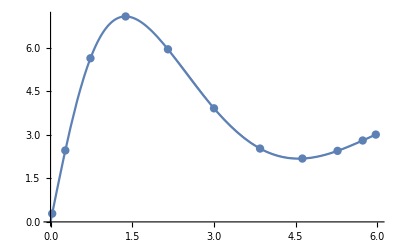

```mathematica
Intf=Interpolation[data];
gr4=Plot[Intf[x],{x,data[[7,1]],6},PlotStyle->Thickness[0.002]];
Show[gr1,gr2,gr4]
(*Построение и вывод интерполирующей фунции при помощи встроенной функции*)
```

```mathematica
{f[2.4316],Pnr[2.4316],Intf[2.4316]}
(*Вычисление значений функции и всех построенных интерполяционных многочленов в точке х=2,4316*)
```

{5.26999,-23038.6,5.29934}

```mathematica
FindMaximum[Abs[f[x]-Intf[x]],{x,1,R}]
(*Нахождение максимума абсолютных погрешнойстей на отрезке*)
```

{0.112247,{x→1.13732}}

### Задание 3

#### Количество точек интерполяции уменьшает погрешность интерполирования. Расположение точек также влияет на результаты интерполирования(равномерное распределение лучше).

### Задание 4

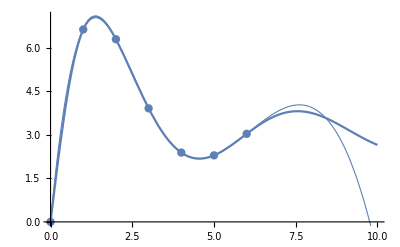

```mathematica
n=6;h=(R-L)/n;
data=N[Table[{L+i*h,f[L+i*h]},{i,0,n}]];
(*Задание нчальных условий*)
Sf=Interpolation[data,Method->"Spline"];
(*Задание интерполяции спайном с помощью встроееного метода*)
gr1=Plot[f[x],{x,0,10}];
gr2=ListPlot[data,PlotStyle->PointSize[0.015]];
gr3=Plot[Sf[x],{x,0,10},PlotStyle->Thickness[0.0020]];
Show[gr1,gr2,gr3]
(*Вывод графика интерполяции спайном*)
```

```mathematica
{f[2.4315],Sf[2.4316]}
(*Вычисление значений функции и всех построенных интерполяционных плайнов в точке х=2,4316*)
```

{5.27024,5.29215}

### Задание 5

3.87677-0.124029 x

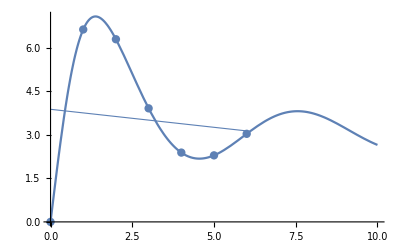

```mathematica
R = LinearSolve[Table[Table[If[i+j==0,∑_(k=1)^(n+1) 1,∑_(k=1)^(n+1) data[[k,1]]^(i+j)],{i,0,1}],{j,0,1}],
Table[If[i==0,∑_(j=1)^(n+1) data[[j,2]],∑_(j=1)^(n+1) (data[[j,2]]*data[[j,1]]^i)],{i,0,1}]];
Pr=0;m=1;
k=0;
While[k<=m,Pr=Pr+R[[k+1]]*x^k; k++];
Q1=Pr
(*Задание многочлена первой степени Q с помощью метода наименьших квадратов*)
gr3=Plot[Q1,{x,0,6},PlotStyle->Thickness[0.002]];
Show[gr1,gr2,gr3]
(*Вывод графика аппроксимации методом наименьших квадратов*)
```

2.29918+1.76908 x-0.315518 x^2

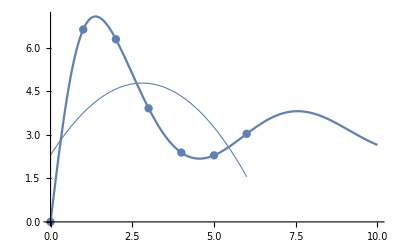

```mathematica
R = LinearSolve[Table[Table[If[i+j==0,∑_(k=1)^(n+1) 1,∑_(k=1)^(n+1) data[[k,1]]^(i+j)],{i,0,2}],{j,0,2}],
Table[If[i==0,∑_(j=1)^(n+1) data[[j,2]],∑_(j=1)^(n+1) (data[[j,2]]*data[[j,1]]^i)],{i,0,2}]];
Pr=0;m=2;
k=0;
While[k<=m,Pr=Pr+R[[k+1]]*x^k; k++];
Q2=Pr
(*Задание многочлена первой степени Q с помощью метода наименьших квадратов*)
gr3=Plot[Q2,{x,0,6},PlotStyle->Thickness[0.002]];
Show[gr1,gr2,gr3]
(*Вывод графика аппроксимации методом наименьших квадратов(многочлен второй степени) *)
```

0.421088+8.02937 x-3.13265 x^2+0.313015 x^3

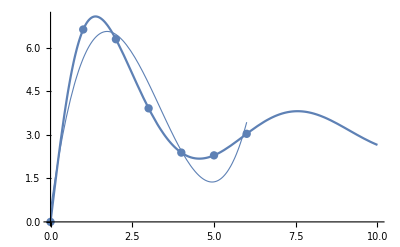

0.00858068+12.0857 x-6.69626 x^2+1.27553 x^3-0.0802098 x^4

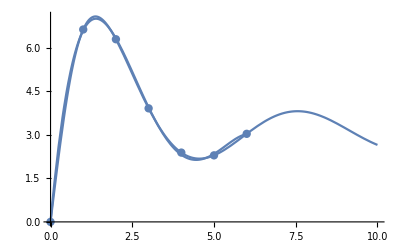

```mathematica
Q3=Fit[data,{1,x,x^2,x^3},x]
(*Нахождение многочлена стреднеквадратичного приближения третьей степени*)
gr3=Plot[Q3,{x,0,6},PlotStyle->Thickness[0.002]];
Show[gr1,gr2,gr3]
(*Вывод графика аппроксимации методом наименьших квадратов(многочлен третьей степени) *)
Q4=Fit[data,{1,x,x^2,x^3,x^4},x]
(*Нахождение многочлена стреднеквадратичного приближения четвертой степени*)
gr4=Plot[Q4,{x,0,6},PlotStyle->Thickness[0.004]];
Show[gr1,gr2,gr4]
(*Вывод графика аппроксимации методом наименьших квадратов(многочлен четвертой степени) *)
```

#### При сравнении результатов, полученных в пунктах а) б) и в) наглядно видно, что увеличение степени среднеквадратичного приближения многочлена приводи к улучшению качества аппроксимации функции